## Transient EWS - Seasonal Ricker - bifurcation rb

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/ricker_seasonal_coe"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,30,10,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)
bl=1;
bh=3.5; (* realisation nuber for individual trajectory and power spectrum evolution *)
relNum=3;
rw=0.4 ;(* rolling window *)
```

## Import Data

```mathematica
(* specific directory *)
direc="ricker_trans_rb";
```

```mathematica
ewsSingles=Import["data_export/"<>direc<>"/ews_singles.csv"];
specData=Import["data_export/"<>direc<>"/pspecs.csv"];
```

```mathematica
tmax=Max[ewsSingles[[2;;,3]]];
dt2=ewsSingles[[3,3]]-ewsSingles[[2,3]];
windowComps=rw*tmax/dt2-1;
```

## General figure options

```mathematica
opts={LabelStyle->12,
Joined->True,
Frame->True,
ImageSize->400};
```

## Trajectory Plots

```mathematica
(* columns *)
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Coherence factor,Params fold,Params hopf,Params null,Smax,Smax/Var,Cross correlation}

```mathematica
xSeries=Cases[ewsSingles[[;;,{1,2,3,4}]],{relNum,"x",_,_}][[;;,{3,4}]];
ySeries=Cases[ewsSingles[[;;,{1,2,3,4}]],{relNum,"y",_,_}][[;;,{3,4}]];
```

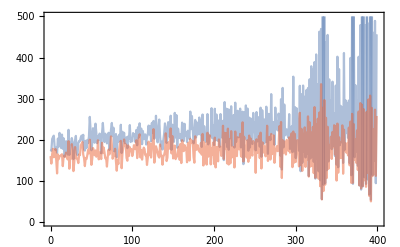

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[{xSeries,ySeries},
opts,
PlotStyle->{Directive[TMBcolours[[1]],Opacity[0.5]],Directive[TMBcolours[[4]],Opacity[0.5]]},
PlotRange->{{0,400},{0,500}}]
```

## Bifurcation Diagram

```mathematica
(* Import bifurcation data *)
bifDataX= Import["data_export/bif_data/bif_rb_x.csv"]; (* pop post breeding period *)
bifDataY= Import["data_export/bif_data/bif_rb_y.csv"]; (* pop post non-breeding period *)
```

```mathematica
(* Extract growth (r) values and state values *)
rVals=bifDataX[[1,2;;]];
stateValsX=bifDataX[[2;;,2;;]];
stateValsY=bifDataY[[2;;,2;;]];
```

```mathematica
bifDataX//Dimensions
```

{101,1001}

```mathematica
(* Compute corresponding time values for each r value *)
tbifVals=(bl-rVals)*tmax/(bl-bh);
```

```mathematica
(* Arrange for plotting *)
plotValsX=Table[Transpose[{tbifVals,stateValsX[[i]]}],{i,1,Length[stateValsX]}];
plotValsY=Table[Transpose[{tbifVals,stateValsY[[i]]}],{i,1,Length[stateValsX]}];
```

```mathematica
bifRickerY=ListPlot[plotValsY[[-10;;,;;]],
FrameLabel->{{"Population size",None},{"Time",None}},
PlotRange->{{0,400},{0,500}},
PlotStyle->Directive[{Darker[TMBcolours[[4]],0.2],PointSize[0.005]}]];
```

```mathematica
bifRickerX=ListPlot[plotValsX[[-10;;,;;]],
Joined->False,
opts,
FrameLabel->{{"Population size",None},{"Time",None}},
PlotRange->{{0,tmax+1},{0,500}},
PlotStyle->Directive[{Darker[TMBcolours[[1]],0.2],PointSize[0.005]}]];
```

### Output

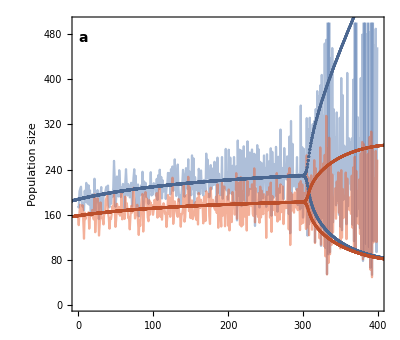

```mathematica
bifTrajPlot=Show[{plotX,bifRickerX,bifRickerY},
opts,
PlotRange->{{0,tmax+1},{0,500}},
FrameLabel->{{"Population size",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
AspectRatio->0.85,
Epilog->{Text[Style["a",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle]},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

## Single EWS Plots

### Variance

```mathematica
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,AIC fold,AIC hopf,AIC null,Coherence factor,Params fold,Params hopf,Params null,Smax,Smax/Var,Cross correlation}

```mathematica
seriesX=Table[
Cases[
ewsSingles[[2;;,{1,2,3,8}]],
{i,"x",_,_}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
seriesY=Table[
Cases[
ewsSingles[[2;;,{1,2,3,8}]],
{i,"y",_,_}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
varPlotY=ListLinePlot[seriesY,
opts,
PlotRange->{{0,tmax+1},All},
PlotStyle->TMBcolours[[4]],
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{Transpose[{Range[0,10,2]*10^(-1),Range[0,10,2]}],Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
(*Text[Style["×10^-1",14],indexPos],*)
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}];
```

```mathematica
varPlotX=ListLinePlot[seriesX,
opts,
PlotRange->{{0,tmax+1},All},
PlotStyle->TMBcolours[[1]],
FrameLabel->{{"Var",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{Transpose[{Range[0,10,2]*10^(-1),Range[0,10,2]}],Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
(*Text[Style["×10^-1",14],indexPos],*)
Text[Style["b",14,Bold],Scaled[labelLetterPos]]}];
```

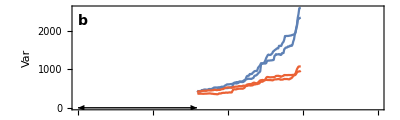

```mathematica
plotVar=Show[varPlotX,varPlotY]
```

### Autocorrelation and Cross correlation

```mathematica
indexCross=Position[ewsSingles[[1]],"Cross correlation"][[1,1]];
```

```mathematica
seriesX=Table[
Cases[
ewsSingles[[2;;,{1,2,3,9}]],
{i,"x",_,_}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
seriesY=Table[
Cases[
ewsSingles[[2;;,{1,2,3,9}]],
{i,"y",_,_}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
seriesCross=Table[
Cases[
ewsSingles[[2;;,{1,2,3,indexCross}]],
{i,"x",_,_}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
ymin=-1;
ymax=1;
```

```mathematica
plotAcX=ListLinePlot[seriesX,
opts,
FrameLabel->{{"Lag-1 AC","Cross correlation"},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax+1},{ymin,ymax}},
PlotStyle->TMBcolours[[1]],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}];
```

```mathematica
plotAcY=ListLinePlot[seriesY,
opts,
FrameLabel->{{"Lag-τ AC","Cross correlation"},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax+1},{ymin,ymax}},
PlotStyle->TMBcolours[[4]],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}];
```

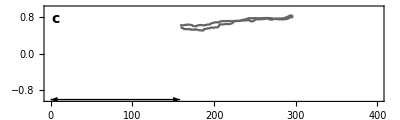

```mathematica
plotCross=ListLinePlot[seriesCross,
opts,
FrameLabel->{{"","Cross correlation"},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax+1},{ymin,ymax}},
PlotStyle->GrayLevel[0.4],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}],
Text[Style["c",14,Bold],Scaled[labelLetterPos]]}]
```

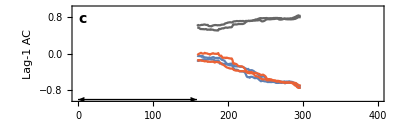

```mathematica
plotAc=Show[plotAcX,plotAcY,plotCross]
```

### Smax

```mathematica
index=Position[ewsSingles[[1]],"Smax"][[1,1]]
```

22

```mathematica
seriesX=Table[
Cases[
ewsSingles[[2;;,{1,2,3,index}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
seriesY=Table[
Cases[
ewsSingles[[2;;,{1,2,3,index}]],
{i,"y",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
plotSmaxX=ListPlot[seriesX,
opts,
PlotRange->{{0,tmax+1},All},
PlotStyle->TMBcolours[[1]],
FrameLabel->{{"S_max",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{Transpose[{10^(-1)*Range[0,10,1],Range[0,10,1]}],Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
(*Text[Style["×10^-1",14],indexPos],*)
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}];
```

```mathematica
plotSmaxY=ListPlot[seriesY,
opts,
PlotRange->{{0,tmax+1},All},
PlotStyle->TMBcolours[[4]],
FrameLabel->{{"S_max",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{Transpose[{10^(-1)*Range[0,10,1],Range[0,10,1]}],Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
(*Text[Style["×10^-1",14],indexPos],*)
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}];
```

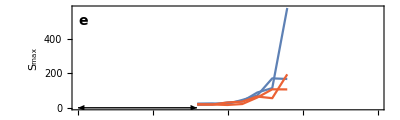

```mathematica
plotSmax=Show[plotSmaxX,plotSmaxY]
```

### AIC

```mathematica
index=Position[ewsSingles[[1]],"AIC hopf"][[1,1]]
```

16

```mathematica
seriesX=Table[
Cases[
ewsSingles[[relNum;;,{1,2,3,index}]],
{i,"x",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
seriesY=Table[
Cases[
ewsSingles[[relNum;;,{1,2,3,index}]],
{i,"y",_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,2}];
```

```mathematica
plotAICX=ListLinePlot[seriesX,
opts,
PlotRange->{{0,tmax+1},{-0.05,1.05}},
PlotStyle->TMBcolours[[1]],
FrameLabel->{{"ω_flip",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}];
```

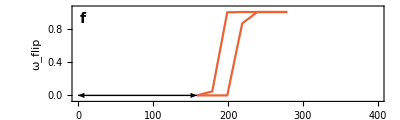

```mathematica
plotAICY=ListLinePlot[seriesY,
opts,
PlotRange->{{0,tmax+1},{-0.05,1.05}},
PlotStyle->TMBcolours[[4]],
FrameLabel->{{"ω_flip",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{40,padTop}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps*dt2,0}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}]
```

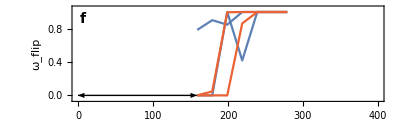

```mathematica
plotAIC=Show[plotAICX,plotAICY]
```

### Power Spectrum

```mathematica
specData//Dimensions
```

{5671,5}

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specData[[2;;,3]]]
```

{159.,179.,199.,219.,239.,259.,279.}

```mathematica
pspecsX=Table[
Cases[specData,
{relNum,"x",i,_,_}]⟦;;,{4,5}⟧,
{i,plotTimes}];
```

```mathematica
pspecsY=Table[
Cases[specData,
{relNum,"y",i,_,_}]⟦;;,{4,5}⟧,
{i,plotTimes}];
```

```mathematica
(* loop power spectrum for display *)
ωVals=pspecsX[[1,;;,1]];
ωValsExt={ωVals-2Pi,ωVals,ωVals+2Pi}//Flatten;
pspecsXExt=Table[
Transpose[{ωValsExt,Join[pspecsX[[i,;;,2]],pspecsX[[i,;;,2]],pspecsX[[i,;;,2]]]}],
{i,1,Length[pspecsX]}];
pspecsYExt=Table[
Transpose[{ωValsExt,Join[pspecsY[[i,;;,2]],pspecsY[[i,;;,2]],pspecsY[[i,;;,2]]]}],
{i,1,Length[pspecsY]}];

(* now trim values *)
len=Dimensions[pspecsExt][[2]];
pspecsXExt=pspecsXExt[[;;,20;;-20]];
pspecsYExt=pspecsYExt[[;;,20;;-20]];
```

```mathematica
colFunX[z_]:=Blend[{Lighter[TMBcolours[[1]],0.9],Darker[TMBcolours[[1]],0.1]},(z-timeRange[[1]])/(timeRange[[2]]-timeRange[[1]])]
colFunY[z_]:=Blend[{Lighter[TMBcolours[[4]],0.9],Darker[TMBcolours[[4]],0.1]},(z-timeRange[[1]])/(timeRange[[2]]-timeRange[[1]])]
```

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegendX=BarLegend[{colFunX[#]&,timeRange},LegendLabel->Style["Time",12],LegendMarkerSize->100];
colLegendY=BarLegend[{colFunY[#]&,timeRange},LegendLabel->Style["Time",12],LegendMarkerSize->100];
```

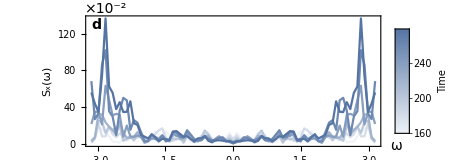

```mathematica
(* plot of power spectra *)
plotPspecX=ListLinePlot[pspecsX,
PlotRange->{{-Pi,Pi},All},
PlotStyle->(colFunX[#]&/@plotTimes),
opts,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{5,2}},
AspectRatio->0.4,
FrameLabel->{{"S_x(ω)",None},{None,None}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
PlotRangeClipping->True,
Epilog->{Text[Style["×10^-2",14],Scaled[{0.065,1.05}]],
Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Text[Style["ω",14],Scaled[{1.05,0}]],
Inset[colLegendX,Scaled[{0.6,0.5}]]}
(*FrameTicks->{{Transpose[{Range[0,20,1]*10,Range[0,20,1]}],None},{Automatic,None}}*)]
```

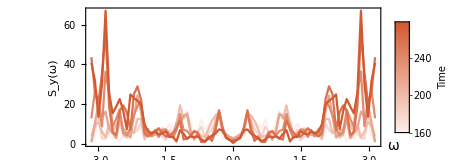

```mathematica
(* plot of power spectra for y *)
plotPspecY=ListLinePlot[pspecsY,
PlotRange->{{-Pi,Pi},All},
PlotStyle->(colFunY[#]&/@plotTimes),
opts,
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{2*padBottom,2}},
AspectRatio->0.4,
FrameLabel->{{"S_y(ω)",None},{None,None}},
(*FrameTicks->{{Range[0,5,1],Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False,
Epilog->{(*Text[Style["×10^-2",14],Scaled[{0.065,1.05}]]*)
(*Text[Style["d",14,Bold],Scaled[{0.035,0.93}]]*)
Text[Style["ω",14],Scaled[{1.04,0}]],
Inset[colLegendY,Scaled[{0.6,0.5}]]}
(*FrameTicks->{{Transpose[{Range[0,20,1]*10,Range[0,20,1]}],None},{Automatic,None}}*)]
```

```mathematica
plotPspec=GraphicsColumn[{plotPspecX,plotPspecY},Spacings->{0,-15}];
```

## Grid: Single EWS

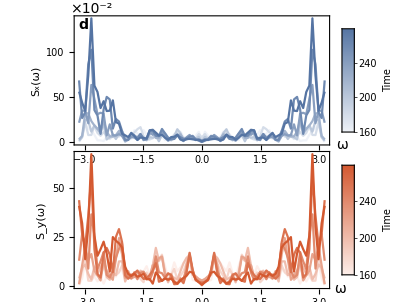
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
 | 
 |

```mathematica
gridPlot=Grid[{{bifTrajPlot,plotPspec},{plotVar,plotSmax},{plotAc,plotAIC},{},{}},Spacings->{-1.5,0}]
```

```mathematica
(*Export["figures/ews_trans_rb.png",gridPlot,ImageResolution->200];*)
```